```mathematica
fc[a_,r_]:=Module[ {ix},

(* create random selection of an arm *)
ix= RandomChoice[Range[1,Length[a]]];

(* compute the reward at this index *)
{ix,RandomVariate[Part[a,ix]]}
];

fg[a_,r_]:=Module[ {ix},

(* compute index for max reward *)
ix= Flatten@Position[r,Max@r];

(* if multiple distributins returned choose one randomly *)
ix = Part[ix,RandomChoice@Range@Length@ix];

(* return index and random sample from distribution *)
{ix,RandomVariate[Part[a,ix]]}
];

play[eps_]:=RandomChoice[{eps,1-eps}-> {fc,fg}] ;

updateRewards[ix_,v_, r_,c_]:=Module[{rr=r,cc=c},

(* if no rewards yet for this arm *)
If[cc[[ix]]==0,

(* then init rewards with value *)
rr[[ix]]=v,

(* otherwise, iteratively update the mean reward for this arm *)
rr[[ix]] = rr[[ix]] + (1/(cc[[ix]]+1))*(v-rr[[ix]]);
];

(* update arm selection count *)
cc[[ix]] = cc[[ix]] + 1;

(* that's all *)
{rr,cc}
];
```

```mathematica
expt[nArms_,eps_,nPlays_]:= Module[{rewards,counts,armMeans,arms,result},

(* init arm rewards and selection counts to zero *)
rewards = ConstantArray[0,nArms];
counts   = ConstantArray[0,nArms];

(* generate mean value for each arm distribution *)
armMeans = RandomVariate[NormalDistribution[],nArms];

(* generate normal distribution with armMeans and std=1 for each arm*)
arms = Map[NormalDistribution[#,1]&,armMeans];

(* make a play, update the rewards and counts, repeat ... *)
Flatten@Table[{
result = play[eps][arms,rewards];
{rewards,counts} = updateRewards[result[[1]],result[[2]],rewards,counts];
result[[2]]
},{i,1,nPlays}]
];
```

```mathematica
trials= Table[ParallelTable[expt[10,eps,1000],{i,1,2000}],{eps,{0,0.01,0.1}}];
```

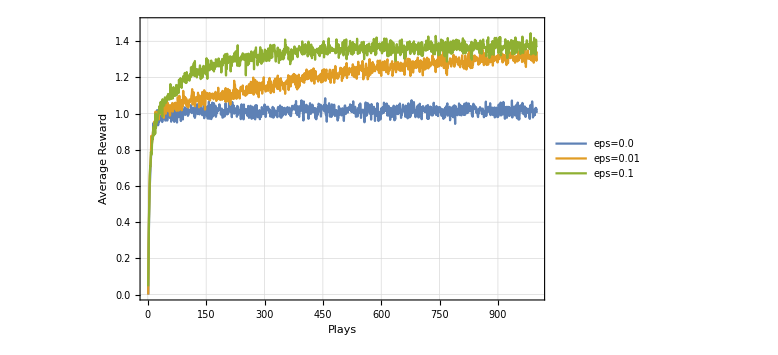

```mathematica
p = Show[
  ListLinePlot[Mean/@trials, 
PlotLegends->{"eps=0.0","eps=0.01","eps=0.1"},
GridLines->Automatic,
ImageSize-> Large,
PlotRange->{0,1.5}],
  FrameLabel->{
Style["Plays"                     ,FontSize->14],
Style["Average Reward",FontSize->14]
},
Frame->True
]
```